# XPS

## Loading Stuffs I might need

```mathematica
ClearSystemCache[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<ErrorBarPlots`
```

```mathematica
<<PhysicalConstants`
```

## Helper Functions

### Reading in the data and doing stuff on it

This reads the data files from the Auger experiment, it’s two rows of data and the first 8 lines are pretty much useless comments

```mathematica
ClearAll[ReadRawData]
ReadRawData[file_]:=ReadList[file,{Real,Real,Real}]
```

```mathematica
ClearAll[AllDataFiles]
AllDataFiles[path_]:=FileNames["./data/"~~path~~"/*.dat"]
```

Selects data points in a certain x interval

```mathematica
ClearAll[TakeRegion]
TakeRegion[data_,min_,max_]:=Select[data,#⟦1⟧≥min&& #⟦1⟧≤max&]
```

```mathematica
ClearAll[Around]
Around[data_,value_]:=First[Nearest[First[dataᵀ],value]]
```

```mathematica
ClearAll[DropMiddle]
DropMiddle[data_]:=Reverse[{dataᵀ⟦1⟧,dataᵀ⟦3⟧}ᵀ]
```

### Fitting stuff

```mathematica
ClearAll[GaussPeakFit]
GaussPeakFit[data_,{min_,max_}]:=Module[{region,midpoint,maxheight},
region=Select[data,First[#]≥min&& First[#]≤max&];
midpoint=Round[(min+max)/2];
maxheight=Min[region⟦All,2⟧];
NonlinearModelFit[region,A*Exp[(-(x-a)^2)/b]+c,{{A,maxheight},{a,midpoint},b,c},x,MaxIterations->10000]
]
```

```mathematica
ClearAll[GaussDoublePeakFit]
GaussDoublePeakFit[data_,{min_,max_},maxheight1_,maxheight2_,midpoint1_,midpoint2_]:=Module[{region},
region=Select[data,First[#]≥min&& First[#]≤max&];
NonlinearModelFit[region,A1*Exp[(-(x-a1)^2)/b1]+A2*Exp[(-(x-a2)^2)/b2]+c,{{A1,maxheight1},{a1,midpoint1},{A2,maxheight2},{a2,midpoint2},b1,b2,c},x,MaxIterations->10000]
]
```

```mathematica
ClearAll[GaussDoublePeakFitWoC]
GaussDoublePeakFitWoC[data_,{min_,max_},maxheight1_,maxheight2_,midpoint1_,midpoint2_]:=Module[{region},
region=Select[data,First[#]≥min&& First[#]≤max&];
NonlinearModelFit[region,A1*Exp[(-(x-a1)^2)/b1]+A2*Exp[(-(x-a2)^2)/b2],{{A1,maxheight1},{a1,midpoint1},{A2,maxheight2},{a2,midpoint2},b1,b2},x,MaxIterations->10000]
]
```

```mathematica
ClearAll[LorentzPeakFit]
LorentzPeakFit[data_,{min_,max_}]:=Module[{region,midpoint,maxheight},
region=Select[data,First[#]≥min&& First[#]≤max&];
midpoint=Round[(min+max)/2];
maxheight=Min[region⟦All,2⟧];
NonlinearModelFit[region,A/(1+(x-a)^2/b)+c,{{A,maxheight},{a,midpoint},b,c},x,MaxIterations->1000]
]
```

```mathematica
ClearAll[LorentzDoublePeakFit]
LorentzDoublePeakFit[data_,{min_,max_},maxheight1_,maxheight2_,midpoint1_,midpoint2_]:=Module[{region},
region=Select[data,First[#]≥min&& First[#]≤max&];
NonlinearModelFit[region,A1/(1+(x-a1)^2/b1)+A2/(1+(x-a2)^2/b2)+c,{{A1,maxheight1},{a1,midpoint1},{A2,maxheight2},{a2,midpoint2},b1,b2,c},x,MaxIterations->10000]
]
```

```mathematica
ClearAll[LorentzDoublePeakFitWoC]
LorentzDoublePeakFitWoC[data_,{min_,max_},maxheight1_,maxheight2_,midpoint1_,midpoint2_]:=Module[{region},
region=Select[data,First[#]≥min&& First[#]≤max&];
NonlinearModelFit[region,A1/(1+(x-a1)^2/b1)+A2/(1+(x-a2)^2/b2),{{A1,maxheight1},{a1,midpoint1},{A2,maxheight2},{a2,midpoint2},b1,b2},x,MaxIterations->10000]
]
```

### Plotting and shiny stuff

```mathematica
ClearAll[ErrorForm]
ErrorForm[{x_?NumberQ,Δx_?NumberQ},dgts_:2]:=ToString[PaddedForm[N[Round[x,10^(-dgts)]],{dgts+2,dgts}]]<>" ±"<>ToString[PaddedForm[N[Ceiling[Abs[Δx],10^(-dgts)]],{dgts+1,dgts}]]
```

```mathematica
niceStyle={
Axes->True,
Frame->True,
GridLines->Automatic,
ImageSize->600,
ImageMargins->3,
LabelStyle->{16,Bold},
FrameTicksStyle->{Directive[16,Plain],Directive[16,Plain]},
FrameStyle->Thick,
GridLinesStyle->Directive[Dashed,Gray],
AxesStyle->Directive[Dashed,Gray]
};
```

```mathematica
niceStyleWoS={
Axes->True,
Frame->True,
GridLines->Automatic,
ImageMargins->3,
LabelStyle->{16,Bold},
FrameTicksStyle->{Directive[16,Plain],Directive[16,Plain]},
FrameStyle->Thick,
GridLinesStyle->Directive[Dashed,Gray],
AxesStyle->Directive[Dashed,Gray]
};
```

```mathematica
frameTickFunk2[data_,offset_,stepsize_]:={Table[i,{i,offset,Round[Floor[Min[(dataᵀ)⟦1⟧]],100],-stepsize}],Take[Table[i,{i,0,Round[Ceiling[Max[(dataᵀ)⟦1⟧]],100],stepsize}],Length[Table[i,{i,offset,Round[Floor[Min[(dataᵀ)⟦1⟧]],100],-stepsize}]]]}ᵀ
```

```mathematica
(2*10^(Floor[Log10[Round[Ceiling[Max[((silver⟦2⟧)ᵀ)⟦1⟧]],100]-Round[Floor[Min[((silver⟦2⟧)ᵀ)⟦1⟧]],100]]]-1));
```

Part::partd: Part specification silver ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

```mathematica
{Table[i,{i,1250,Round[Floor[Min[((silver⟦2⟧)ᵀ)⟦1⟧]],100],-tickDivide[(silver⟦2⟧),2]}],Take[Table[i,{i,0,50000,tickDivide[(silver⟦2⟧),2]}],Length[Table[i,{i,1250,Round[Floor[Min[((silver⟦2⟧)ᵀ)⟦1⟧]],100],-tickDivide[(silver⟦2⟧),2]}]]]}ᵀ;
```

Part::partd: Part specification silver ⟦ 2 ⟧ is longer than depth of object.

Table::iterb: Iterator {i, 1250, Round[Floor[silver ⟦ 2 ⟧], 100], -tickDivide[silver ⟦ 2 ⟧, 2]} does not have appropriate bounds.

Part::partd: Part specification silver ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Table::iterb: Iterator {i, 0, 50000, tickDivide[silver ⟦ 2 ⟧, 2]} does not have appropriate bounds.

General::stop: Further output of Table :: iterb will be suppressed during this calculation.

Transpose::nmtx: The first two levels of the one-dimensional list {Table[i, {i, 1250, Round[Floor[silver ⟦ 2 ⟧], 100], -tickDivide[silver ⟦ 2 ⟧, 2]}], Table[i, {i, 0, 50000, tickDivide[silver ⟦ 2 ⟧, 2]}]} cannot be transposed.

```mathematica
tickDivide[data_,divisions_]:=(divisions*10^(Floor[Log10[Round[Ceiling[Max[((data)ᵀ)⟦1⟧]],100]-Round[Floor[Min[((data)ᵀ)⟦1⟧]],100]]]-1))
```

```mathematica
frameTickFunk[data_,offset_,divisions_]:={Table[i,{i,offset,Round[Floor[Min[((data)ᵀ)⟦1⟧]],100],-tickDivide[(data),divisions]}],Take[Table[i,{i,0,50000,tickDivide[(data),divisions]}],Length[Table[i,{i,offset,Round[Floor[Min[((data)ᵀ)⟦1⟧]],100],-tickDivide[(data),divisions]}]]]}ᵀ
```

```mathematica
ClearAll[ShowSpectrum]
ShowSpectrum[data_]:=Manipulate[
If[max<min,max=(min+1)];
p=data⟦(min)⟧;
Show[
ListPlot[(data⟦min;;max⟧),PlotRange->All,Joined->joined,Epilog->{Line[{{Dynamic[First[p]],0},{Dynamic[First[p]],Max[data⟦min;;max⟧ᵀ⟦2⟧]}}],Inset[Dynamic[First[p]],{(Dynamic[First[p]]-(max-min)/20),(Dynamic[p⟦2⟧]+(max-min)/20)}]},niceStyle],Graphics[Locator[Dynamic[p]]]
],
{{min,1},(1),(Length[data]-1),1,Appearance->"Labeled"},
{{max,(Length[data])},(min),(Length[data]),1,Appearance->"Labeled"},
{{joined,True},{True,False}},{p,Locator}
]
```

```mathematica
ClearAll[ShowSpectrumBinding]
ShowSpectrumBinding[data_,offset_]:=Manipulate[
If[max<min,max=(min+1)];
p=data⟦(min)⟧;
Show[
ListPlot[(data⟦min;;max⟧),PlotRange->All,Joined->joined,Epilog->{Line[{{Dynamic[First[p]],0},{Dynamic[First[p]],Max[data⟦min;;max⟧ᵀ⟦2⟧]}}],Inset[Dynamic[(offset-First[p])],{(Dynamic[First[p]]-(max-min)/20),(Dynamic[p⟦2⟧]+50)}],Inset[Dynamic[First[p]],{(Dynamic[First[p]]+(max-min)/20),(Dynamic[p⟦2⟧]+50)}]},niceStyle,FrameTicks->{Automatic,Automatic,frameTickFunk[data⟦min;;max⟧,offset,divisions],Automatic}],Graphics[Locator[Dynamic[p]]]
],
{{min,1},(1),(Length[data]-1),1,Appearance->"Labeled"},
{{max,(Length[data])},(min),(Length[data]),1,Appearance->"Labeled"},
{{joined,True},{True,False}},{p,Locator},
{{divisions,2},{1,2,3,5,10,20},Appearance->"DialogBox"}
]
```

```mathematica
ClearAll[CompareSpectrum]
CompareSpectrum[data1_,data2_]:=Manipulate[
p=data1⟦1⟧;
Show[ListPlot[{data1,data2},PlotRange->All,Joined->joined,Epilog->{Line[{{Dynamic[First[p]],0},{Dynamic[First[p]],Max[Join[data1ᵀ⟦2⟧,data2ᵀ⟦2⟧]]}}],Inset[Dynamic[First[p]],{(Dynamic[First[p]]+20),(Dynamic[p⟦2⟧]+20)}]},niceStyleWoS,ImageSize->size],
Graphics[Locator[Dynamic[p]]]
],
{{size,500},500,2000},
{{joined,True},{True,False}},
{p,Locator}
]
```

## Import Data

### Silver

```mathematica
AllDataFiles["Silver"]//TableForm
```

./data/Silver/Ag-Al-50eV-1100-1488_50eV-3runs-333ms-800-Overview.dat
./data/Silver/Ag-Al-50eV-200-1488_50eV-2runs-333ms-1300-Overview.dat
./data/Silver/Ag-Mg-50eV-200-1290eV-3runs-333ms-1100-Overview.dat

```mathematica
silverdata=ReadRawData[#]&/@AllDataFiles["Silver"];
```

```mathematica
silver=DropMiddle[#]&/@silverdata;
```

### Samarium

```mathematica
AllDataFiles["Samarium"]//TableForm
```

./data/Samarium/Sm-Al-25eV-1400-1488_33eV-5runs-333ms-200-FermiOverview.dat
./data/Samarium/Sm-Al-25eV-1450-1499_53eV-30runs-500ms-100-Fermi.dat
./data/Samarium/Sm-Al-25eV-200-1488_30eV-2runs-333ms-1300-Overview.dat
./data/Samarium/Sm-Al-50eV-200-1488_33eV-1runs-333ms-1300-Overview.dat
./data/Samarium/Sm-Al-50eV-200-1488_33eV-7runs-333ms-1300-Overview.dat
./data/Samarium/Sm-Mg-50eV-199_85-14289_84eV-2runs-333ms-1100-Overview.dat

```mathematica
samariumdata=ReadRawData[#]&/@AllDataFiles["Samarium"];
```

```mathematica
samarium=DropMiddle[#]&/@samariumdata;
```

### Coin

```mathematica
AllDataFiles["Coin"]//TableForm
```

./data/Coin/Coin-Al-50eV-200-1488_51eV-5runs-333ms-1300-Overview.dat
./data/Coin/Coin-Mg-50eV-200-1290_02eV-5runs-333ms-1100-Overview.dat

```mathematica
coindata=ReadRawData[#]&/@AllDataFiles["Coin"];
```

```mathematica
coin=DropMiddle[#]&/@coindata;
```

## Silver

```mathematica
AllDataFiles["Silver"]//TableForm
```

./data/Silver/Ag-Al-50eV-1100-1488_50eV-3runs-333ms-800-Overview.dat
./data/Silver/Ag-Al-50eV-200-1488_50eV-2runs-333ms-1300-Overview.dat
./data/Silver/Ag-Mg-50eV-200-1290eV-3runs-333ms-1100-Overview.dat

```mathematica
CompareSpectrum[silver⟦2⟧,silver⟦3⟧]
```

Overview spectrum with magnesium filament

```mathematica
ShowSpectrumBinding[silver⟦3⟧,1248]
```

Overview spectrum with aluminum filament

```mathematica
ShowSpectrumBinding[silver⟦2⟧,1478]
```

Overview spectrum with more runs for energies above 1100

```mathematica
ShowSpectrumBinding[silver⟦1⟧,1478]
```

## Samarium

```mathematica
AllDataFiles["Samarium"]//TableForm
```

./data/Samarium/Sm-Al-25eV-1400-1488_33eV-5runs-333ms-200-FermiOverview.dat
./data/Samarium/Sm-Al-25eV-1450-1499_53eV-30runs-500ms-100-Fermi.dat
./data/Samarium/Sm-Al-25eV-200-1488_30eV-2runs-333ms-1300-Overview.dat
./data/Samarium/Sm-Al-50eV-200-1488_33eV-1runs-333ms-1300-Overview.dat
./data/Samarium/Sm-Al-50eV-200-1488_33eV-7runs-333ms-1300-Overview.dat
./data/Samarium/Sm-Mg-50eV-199_85-14289_84eV-2runs-333ms-1100-Overview.dat

### Overview

```mathematica
CompareSpectrum[samarium⟦6⟧,samarium⟦3⟧]
```

Overview spectrum with aluminum filament with 1 runs at 50eV pass voltage

```mathematica
ShowSpectrum[samarium⟦4⟧]
```

Overview spectrum with aluminum filament with 2 runs at 25eV pass voltage

```mathematica
ShowSpectrum[samarium⟦3⟧]
```

Overview spectrum with aluminum filament with 7 runs at 50eV pass voltage

```mathematica
ShowSpectrumBinding[samarium⟦5⟧,1476.5]
```

Overview spectrum with magnesium filament with 2 runs at 50eV pass voltage

```mathematica
ShowSpectrumBinding[samarium⟦6⟧,1247.5]
```

Fermi edge search with aluminum filament with 5 runs at 25eV pass voltage

```mathematica
ShowSpectrumBinding[samarium⟦3⟧,1476.5]
```

```mathematica
CompareSpectrum[samarium⟦5⟧,samarium⟦6⟧]
```

### Fermi Edge and 4f

Fermi edge with aluminum filament with 30 runs at 25eV pass voltage

```mathematica
ShowSpectrumBinding[samarium⟦2⟧,1476.5]
```

```mathematica
smfit=LorentzDoublePeakFitWoC[samarium⟦2⟧,{1450,1478},185,170,1457.6,1472.5]
```

FittedModel[146.496/(1+0.057995 (-1473.29+x)^2)+178.43/(1+0.0180303 (-«19»+x)^2)]

```mathematica
smfit[{"ParameterTable","RSquared"}]
```

{ | Estimate | Standard Error | t-Statistic | P-Value
A1 | 178.43 | 4.69708 | 37.9874 | 1.51298×10^-38
a1 | 1456.91 | 0.22942 | 6350.42 | 2.42333×10^-149
A2 | 146.496 | 6.35063 | 23.0679 | 2.61687×10^-28
a2 | 1473.29 | 0.1876 | 7853.34 | 5.91314×10^-154
b1 | 55.4623 | 8.0371 | 6.90079 | 8.57932×10^-9
b2 | 17.2429 | 3.35069 | 5.14606 | 4.48004×10^-6,0.990875}

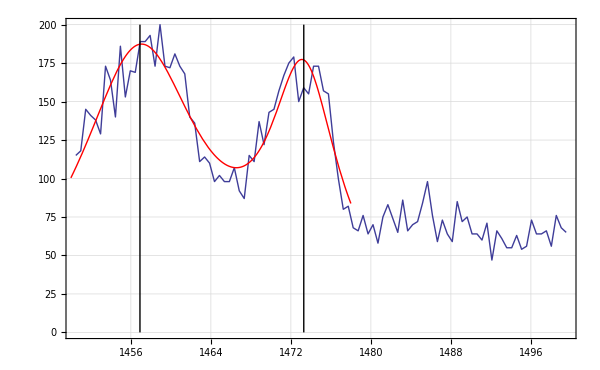

```mathematica
Show[ListLinePlot[samarium⟦2⟧],Plot[Normal[smfit],{x,1450,1478},PlotStyle->Red],niceStyle,FrameTicks->{Automatic,Automatic,frameTickFunk[samarium⟦2⟧,1477,0.5],Automatic},Epilog->{Line[{{1473.29,0},{1473.29,200}}],Line[{{1456.91,0},{1456.91,200}}]}]
```

## Coin

```mathematica
AllDataFiles["Coin"]//TableForm
```

./data/Coin/Coin-Al-50eV-200-1488_51eV-5runs-333ms-1300-Overview.dat
./data/Coin/Coin-Mg-50eV-200-1290_02eV-5runs-333ms-1100-Overview.dat

Overview spectrum with aluminum filament with 5 runs at 50eV pass voltage

```mathematica
ShowSpectrumBinding[coin⟦1⟧,1478]
```

Overview spectrum with magnesium filament with 5 runs at 50eV pass voltage

```mathematica
ShowSpectrumBinding[coin⟦2⟧,1248]
```

```mathematica
CompareSpectrum[coin⟦1⟧,coin⟦2⟧]
```

## Plotting for the talk

### Silver

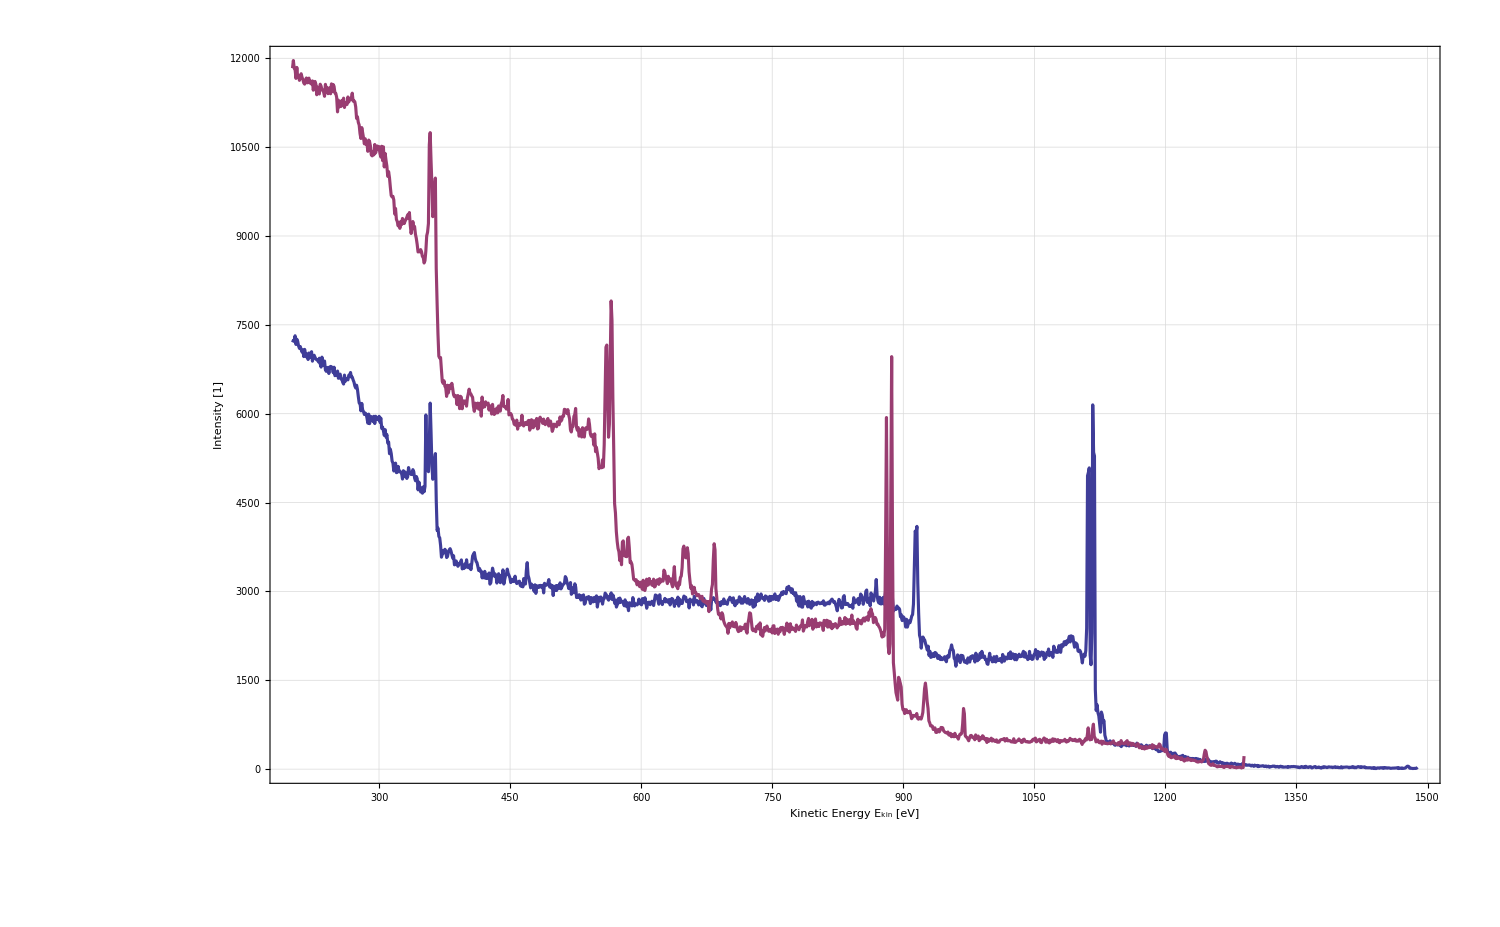

```mathematica
ListLinePlot[{silver⟦2⟧,silver⟦3⟧},niceStyleWoS,ImageSize->1500,PlotStyle->Thickness[0.0015],FrameLabel->{Style["Kinetic Energy E_kin [eV]",Large],Style["Intensity [1]",Large]}]
```

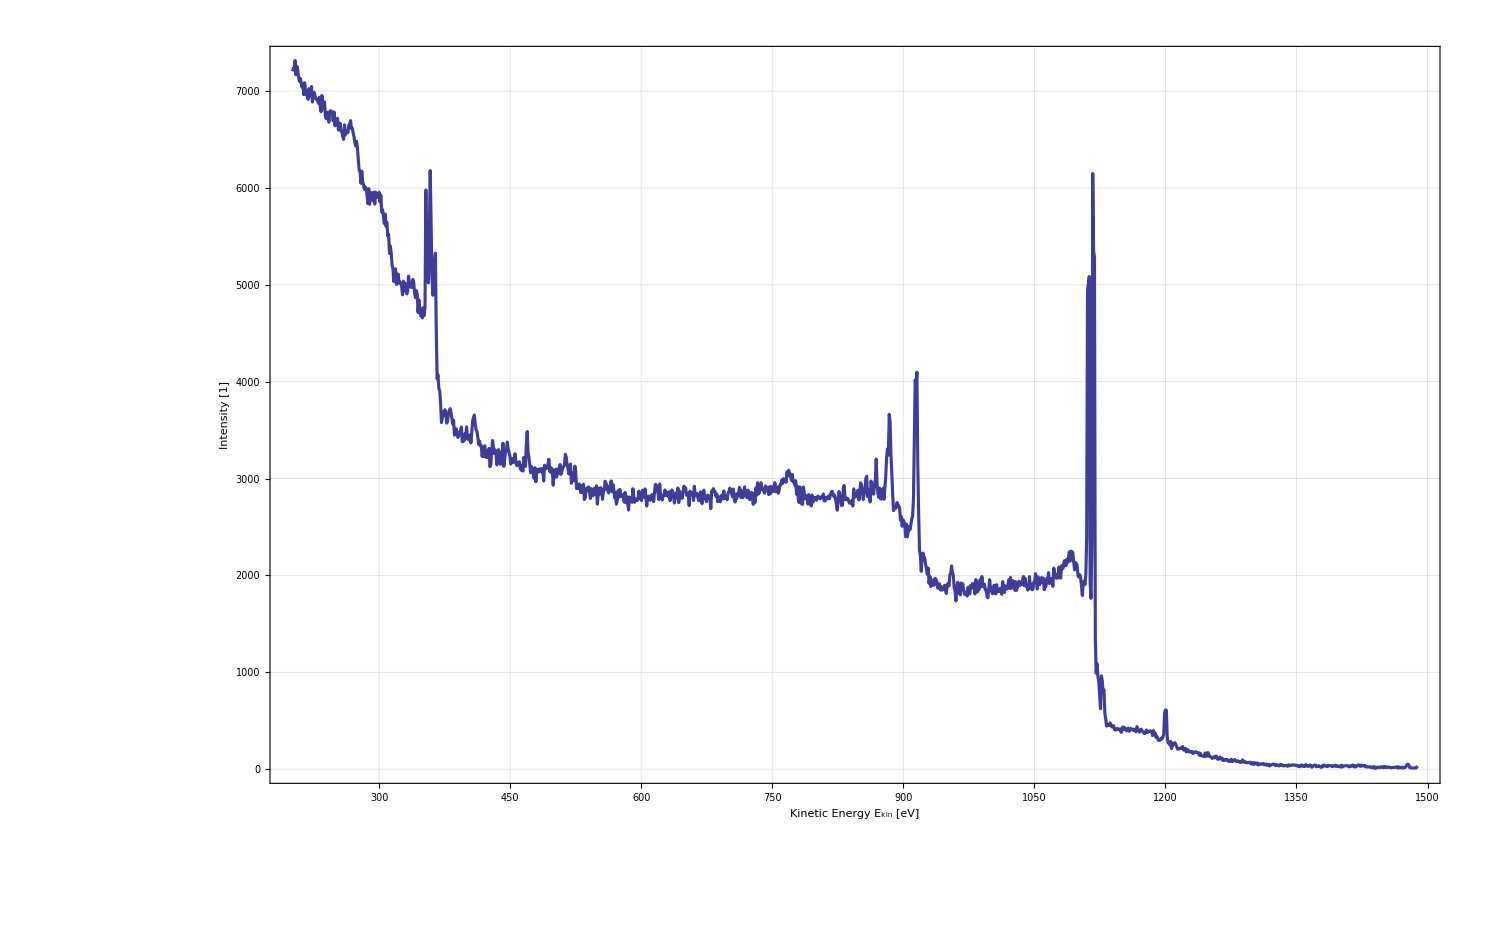

```mathematica
ListLinePlot[silver⟦2⟧,niceStyleWoS,ImageSize->1500,PlotStyle->Thickness[0.0015],FrameLabel->{Style["Kinetic Energy E_kin [eV]",Large],Style["Intensity [1]",Large]}]
```

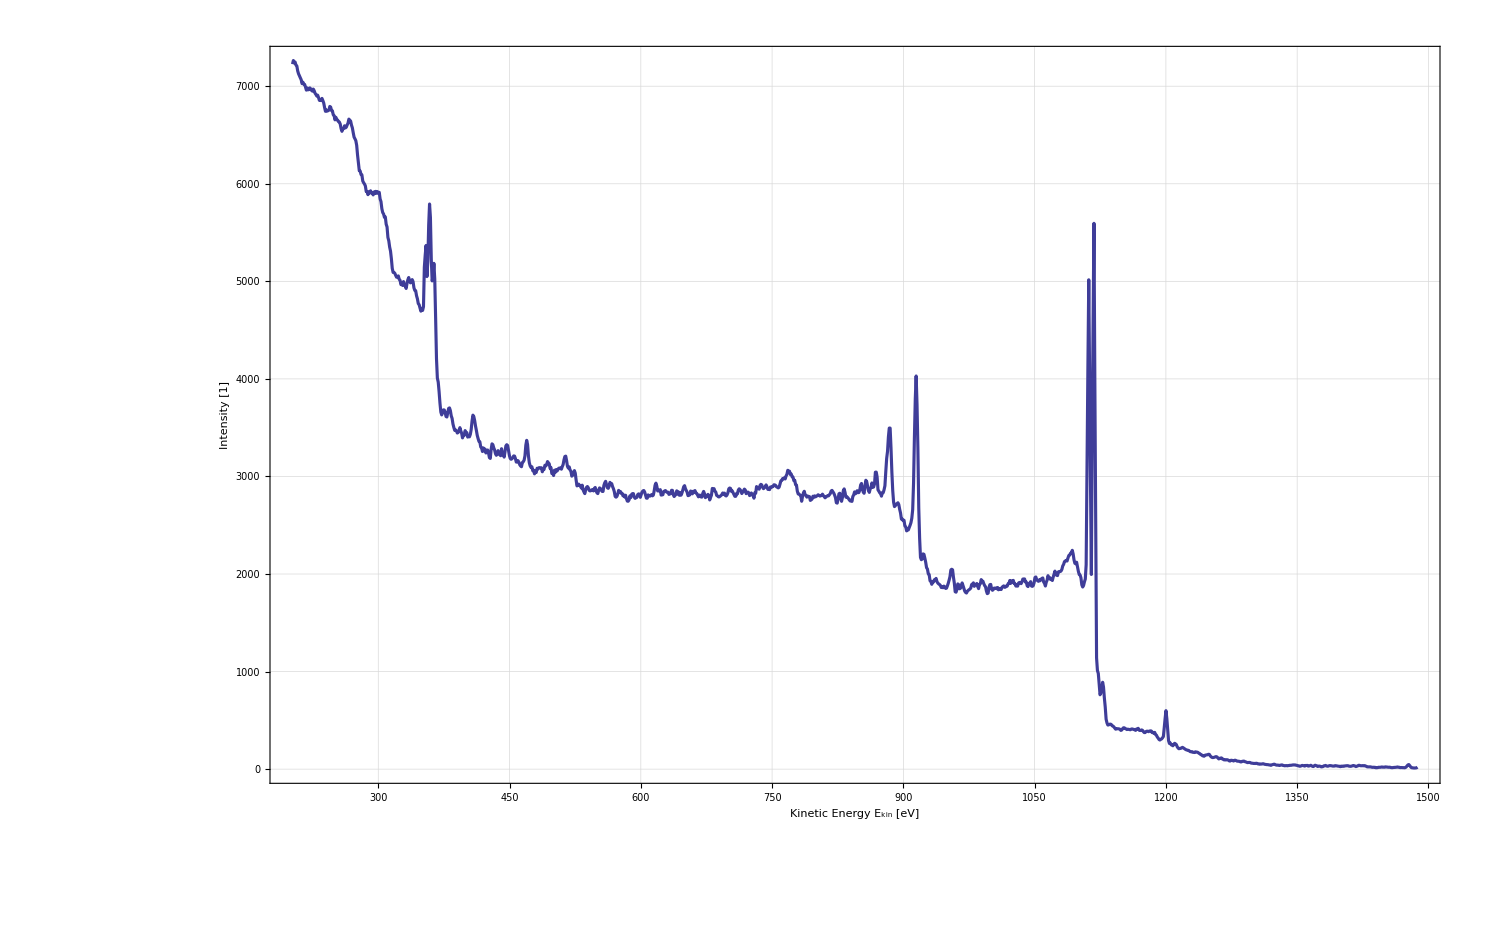

```mathematica
ListLinePlot[MovingAverage[silver⟦2⟧,3],niceStyleWoS,ImageSize->1500,PlotStyle->Thickness[0.0015],FrameLabel->{Style["Kinetic Energy E_kin [eV]",Large],Style["Intensity [1]",Large]}]
```

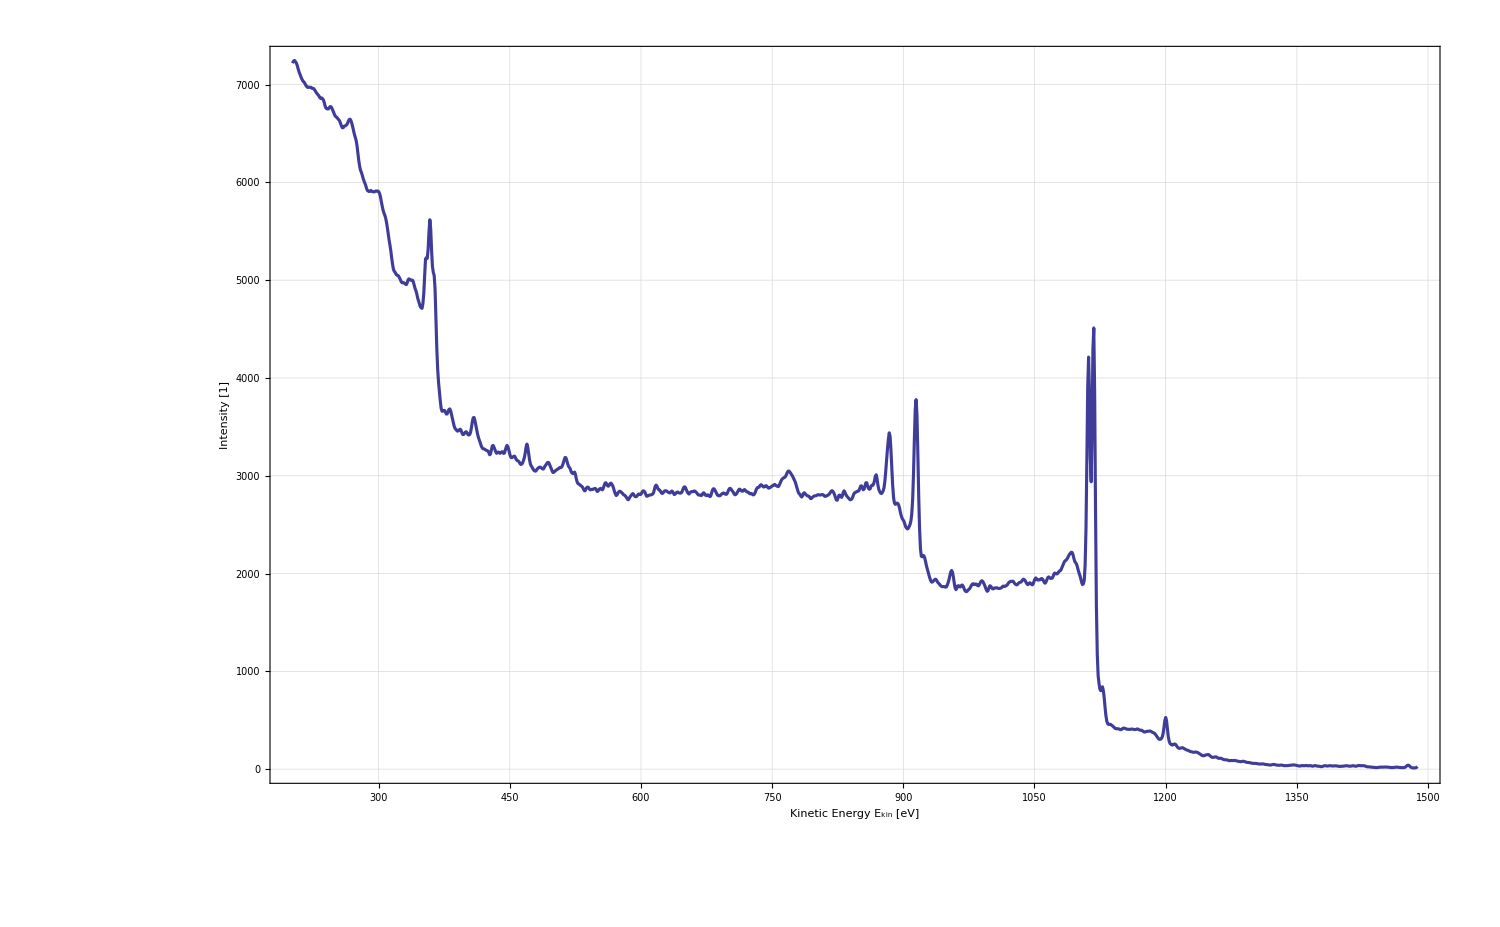

```mathematica
ListLinePlot[{GaussianFilter[silver⟦2⟧ᵀ⟦1⟧,3],GaussianFilter[silver⟦2⟧ᵀ⟦2⟧,3]}ᵀ,niceStyleWoS,ImageSize->1500,PlotStyle->Thickness[0.0015],FrameLabel->{Style["Kinetic Energy E_kin [eV]",Large],Style["Intensity [1]",Large]}]
```

```mathematica
Peak[offset_,string_,x_,y_]:=Inset[Style[string,FontSize->20],{offset-x,y}]
```

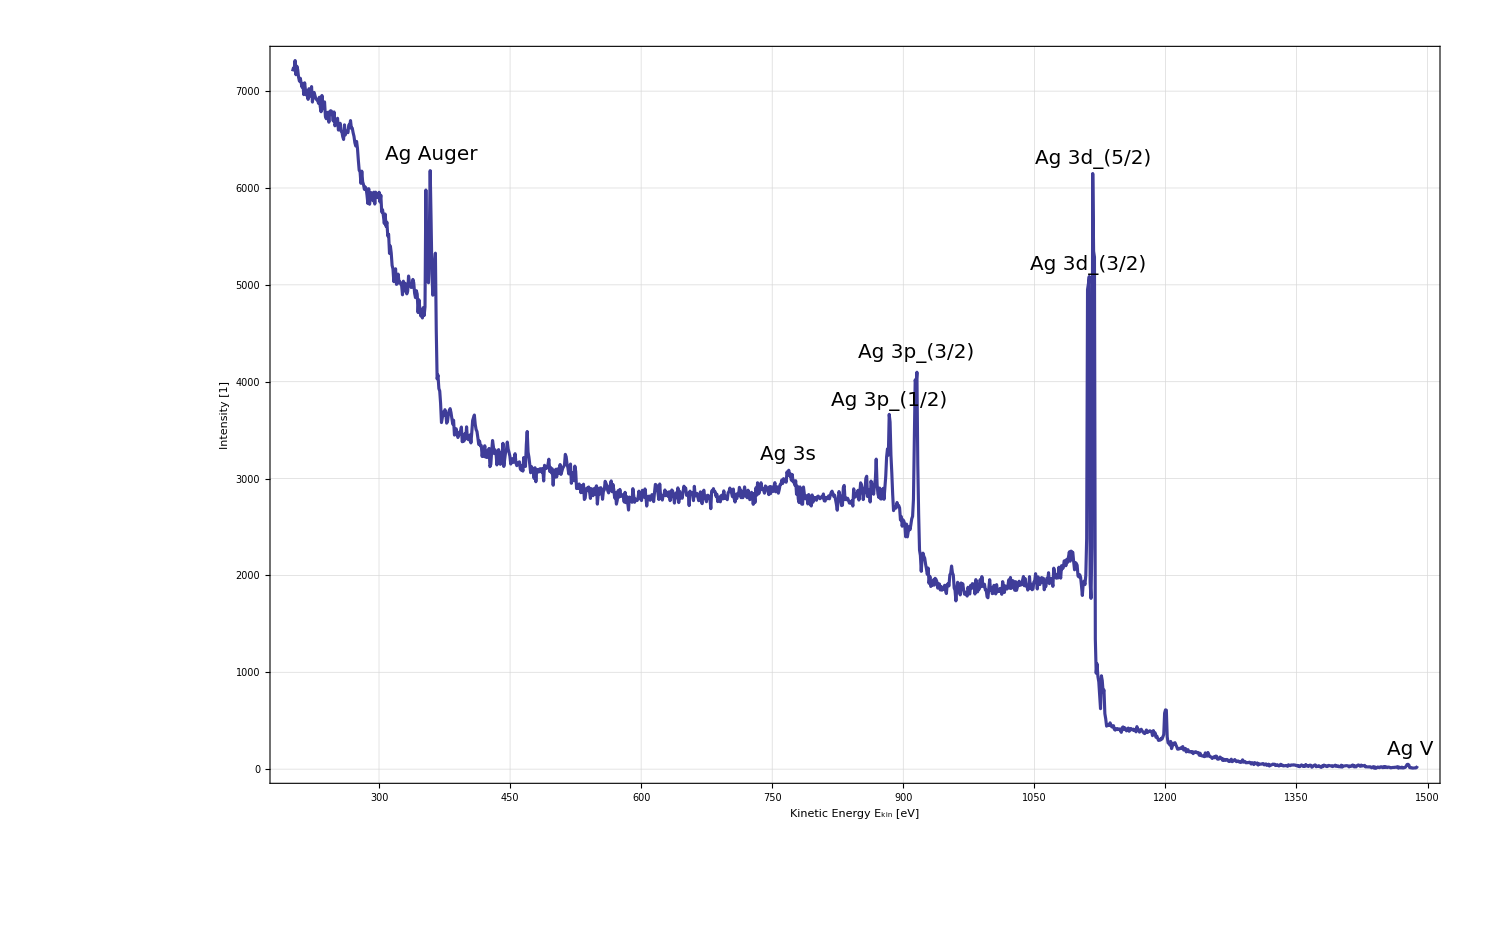

```mathematica
ListLinePlot[silver⟦2⟧,niceStyleWoS,ImageSize->1500,PlotStyle->Thickness[0.0015],FrameTicks->{Automatic,Automatic,frameTickFunk[silver⟦2⟧,1480,2],Automatic},Epilog->(Flatten[{Peak[#,"Ag V",0,200],Peak[#,"Ag 3d_(5/2)",362.5,6300],Peak[#,"Ag 3d_(3/2)",368,5200],Peak[#,"Ag 3p_(3/2)",565.6,4300],Peak[#,"Ag 3p_(1/2)",596,3800],Peak[#,"Ag 3s",712,3250],Peak[#,"Ag Auger",1120,6350]}&/@{1480}]),FrameLabel->{Style["Kinetic Energy E_kin [eV]",Large],Style["Intensity [1]",Large],Style["Binding Energy E_B [eV]",Large],""}]
```

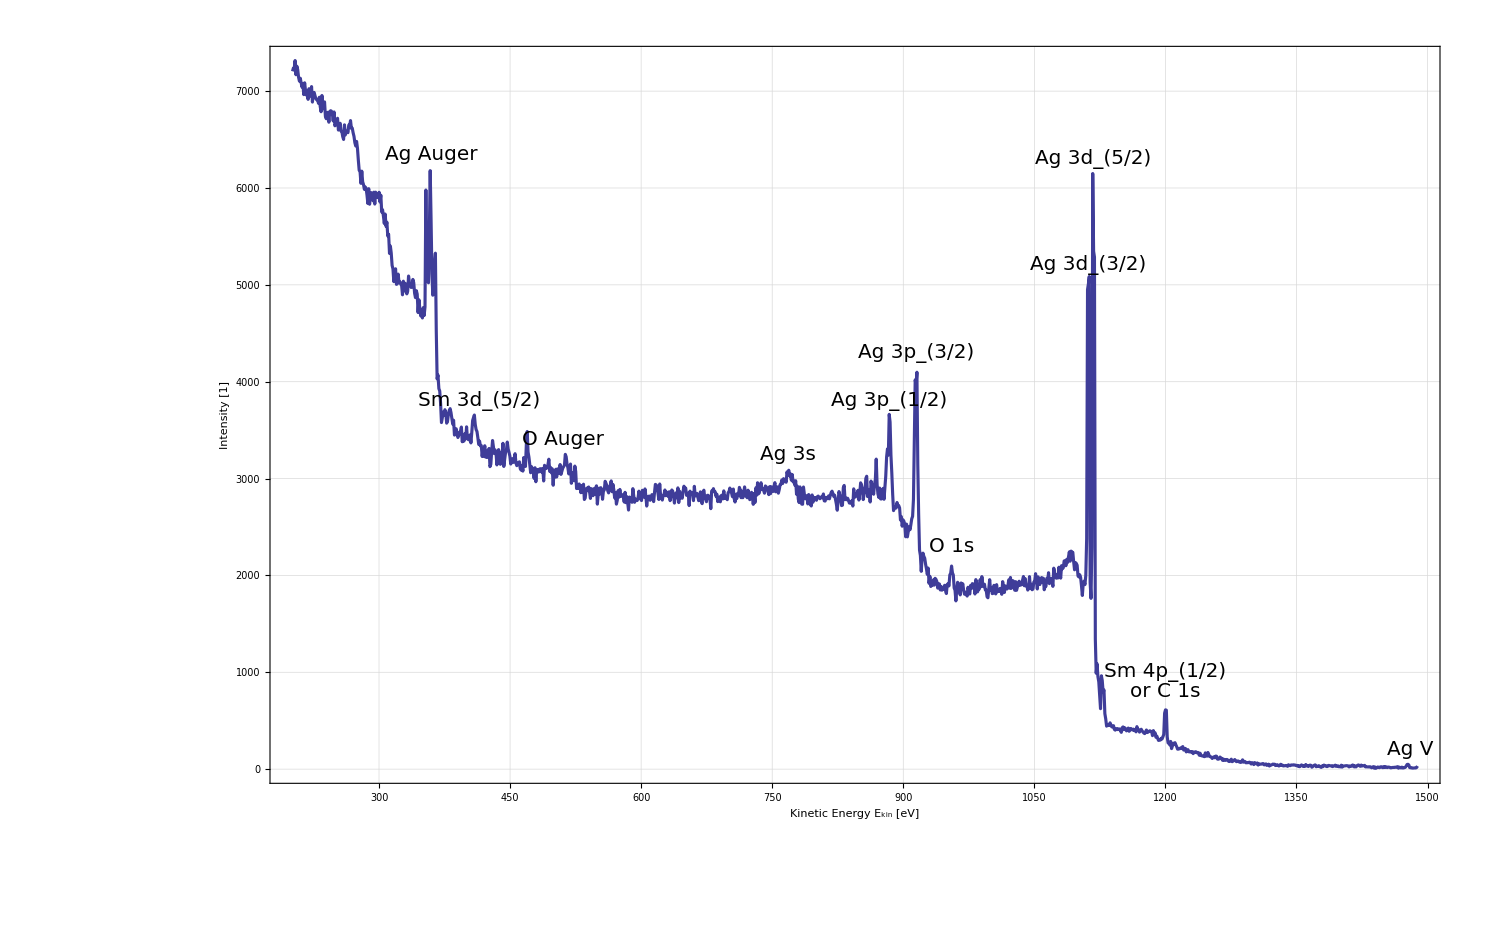

```mathematica
ListLinePlot[silver⟦2⟧,niceStyleWoS,ImageSize->1500,PlotStyle->Thickness[0.0015],FrameTicks->{Automatic,Automatic,frameTickFunk[silver⟦2⟧,1480,2],Automatic},Epilog->(Flatten[{Peak[#,"Ag V",0,200],Peak[#,"Ag 3d_(5/2)",362.5,6300],Peak[#,"Ag 3d_(3/2)",368,5200],Peak[#,"Ag 3p_(3/2)",565.6,4300],Peak[#,"Ag 3p_(1/2)",596,3800],Peak[#,"Ag 3s",712,3250],Peak[#,"Ag Auger",1120,6350],Peak[#,"Sm 4p_(1/2)",280,1000],Peak[#,"or C 1s",280,800],Peak[#,"O 1s",525,2300],Peak[#,"O Auger",969,3400],Peak[#,"Sm 3d_(5/2)",1065,3800]}&/@{1480}]),FrameLabel->{Style["Kinetic Energy E_kin [eV]",Large],Style["Intensity [1]",Large],Style["Binding Energy E_B [eV]",Large],""}]
```

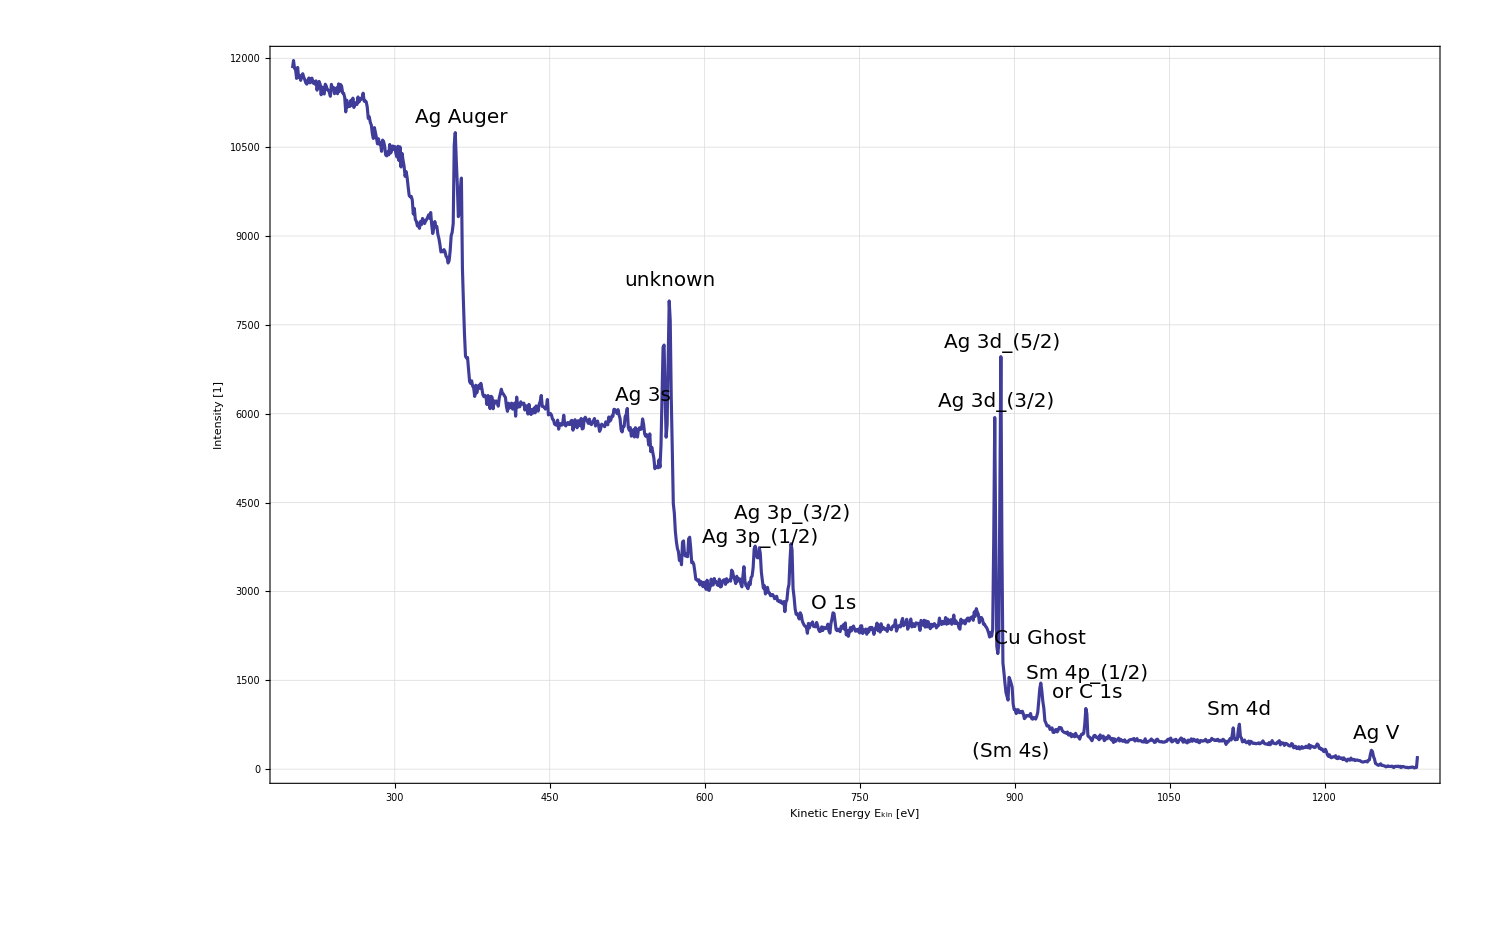

```mathematica
ListLinePlot[silver⟦3⟧,niceStyleWoS,ImageSize->1500,PlotStyle->Thickness[0.0015],FrameTicks->{Automatic,Automatic,frameTickFunk[silver⟦2⟧,1250,2],Automatic},Epilog->(Flatten[{Peak[#,"Ag V",0,600],Peak[#,"(Sm 4s)",354,300],Peak[#,"Ag 3d_(5/2)",362.5,7200],Peak[#,"Ag 3d_(3/2)",368,6200],Peak[#,"O 1s",525,2800],Peak[#,"Ag 3p_(3/2)",565.6,4300],Peak[#,"Ag 3p_(1/2)",596,3900],Peak[#,"Ag 3s",710,6300],Peak[#,"Sm 4p_(1/2)",280,1600],Peak[#,"or C 1s",280,1300],Peak[#,"Cu Ghost",325,2200],Peak[#,"Sm 4d",132.5,1000],Peak[#,"Ag Auger",886,11000],Peak[#,"unknown",684,8250]}&/@{1250}]),FrameLabel->{Style["Kinetic Energy E_kin [eV]",Large],Style["Intensity [1]",Large],Style["Binding Energy E_B [eV]",Large],""}]
```

### Samarium

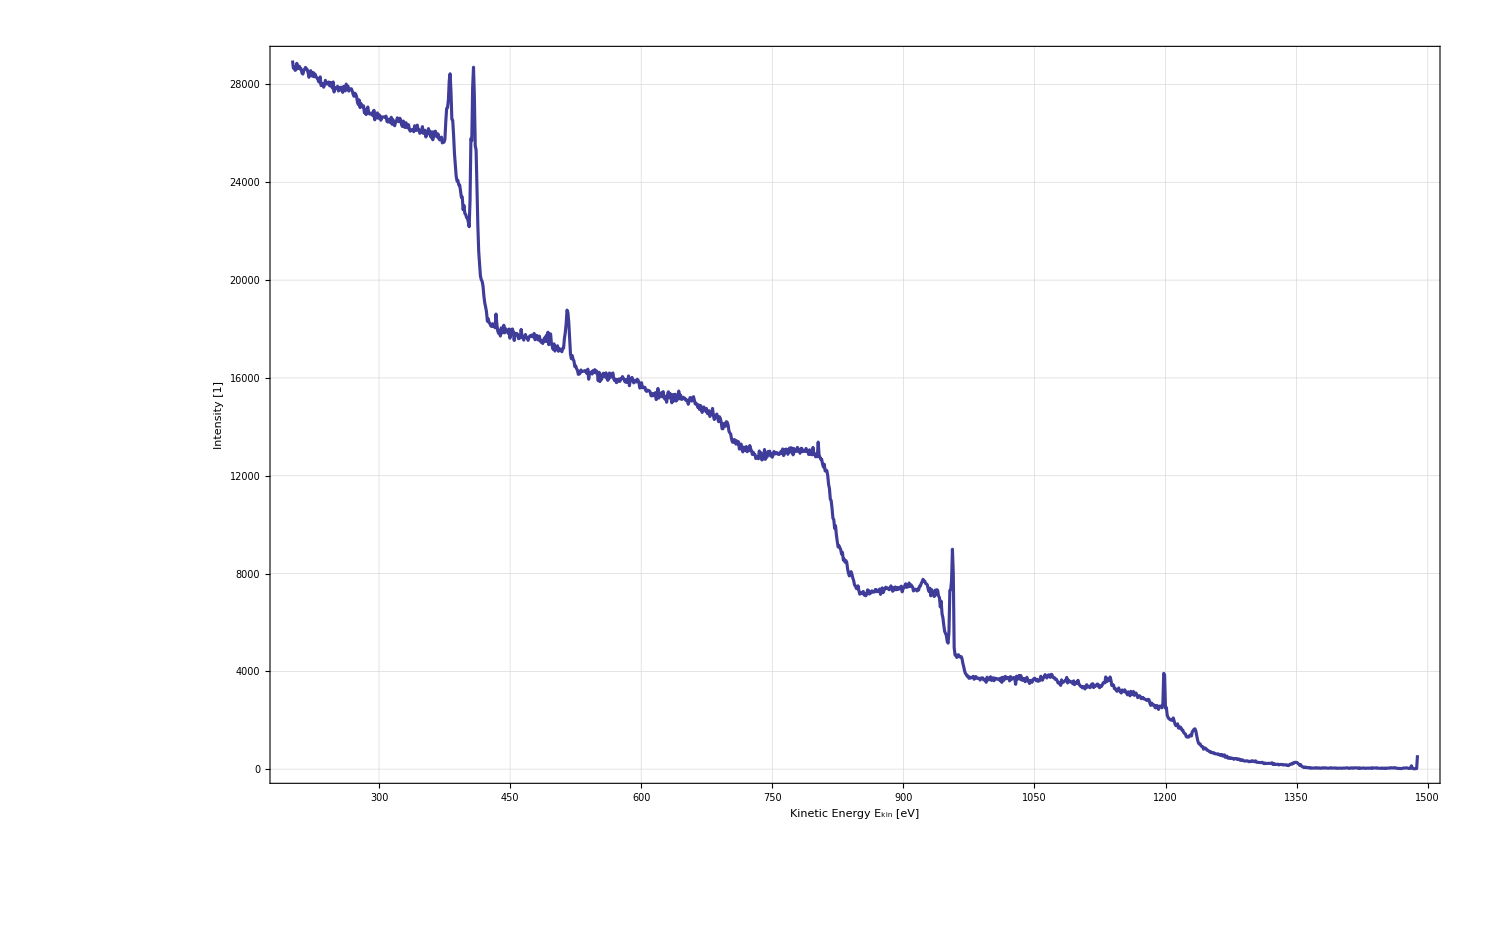

```mathematica
ListLinePlot[samarium⟦5⟧,niceStyleWoS,ImageSize->1500,PlotStyle->Thickness[0.0015],FrameLabel->{Style["Kinetic Energy E_kin [eV]",Large],Style["Intensity [1]",Large]}]
```

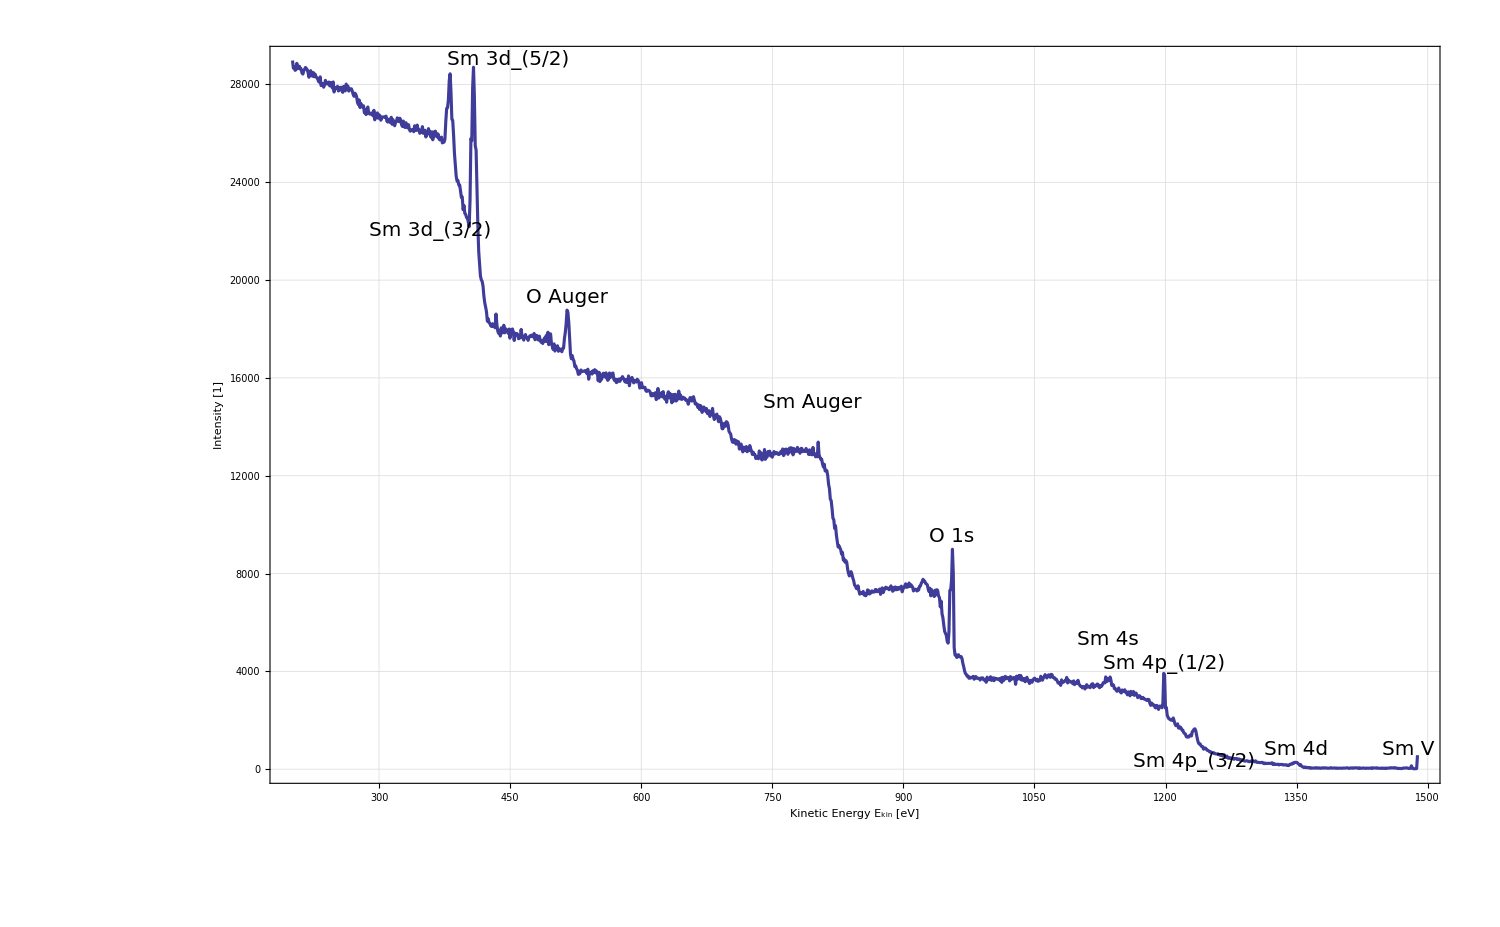

```mathematica
ListLinePlot[samarium⟦5⟧,niceStyleWoS,ImageSize->1500,PlotStyle->Thickness[0.0015],FrameTicks->{Automatic,Automatic,frameTickFunk[samarium⟦5⟧,1478,2],Automatic},Epilog->(Flatten[{Peak[#,"Sm V",0,800],Peak[#,"Sm 4d",129,800],Peak[#,"Sm 4p_(3/2)",245,300],Peak[#,"Sm 4p_(1/2)",279.5,4300],Peak[#,"Sm 4s",344,5300],Peak[#,"O 1s",523,9500],Peak[#,"Sm Auger",682,15000],Peak[#,"O Auger",963,19300],Peak[#,"Sm 3d_(5/2)",1030,29000],Peak[#,"Sm 3d_(3/2)",1120,22000]}&/@{1478}]),FrameLabel->{Style["Kinetic Energy E_kin [eV]",Large],Style["Intensity [1]",Large],Style["Binding Energy E_B [eV]",Large],""}]
```

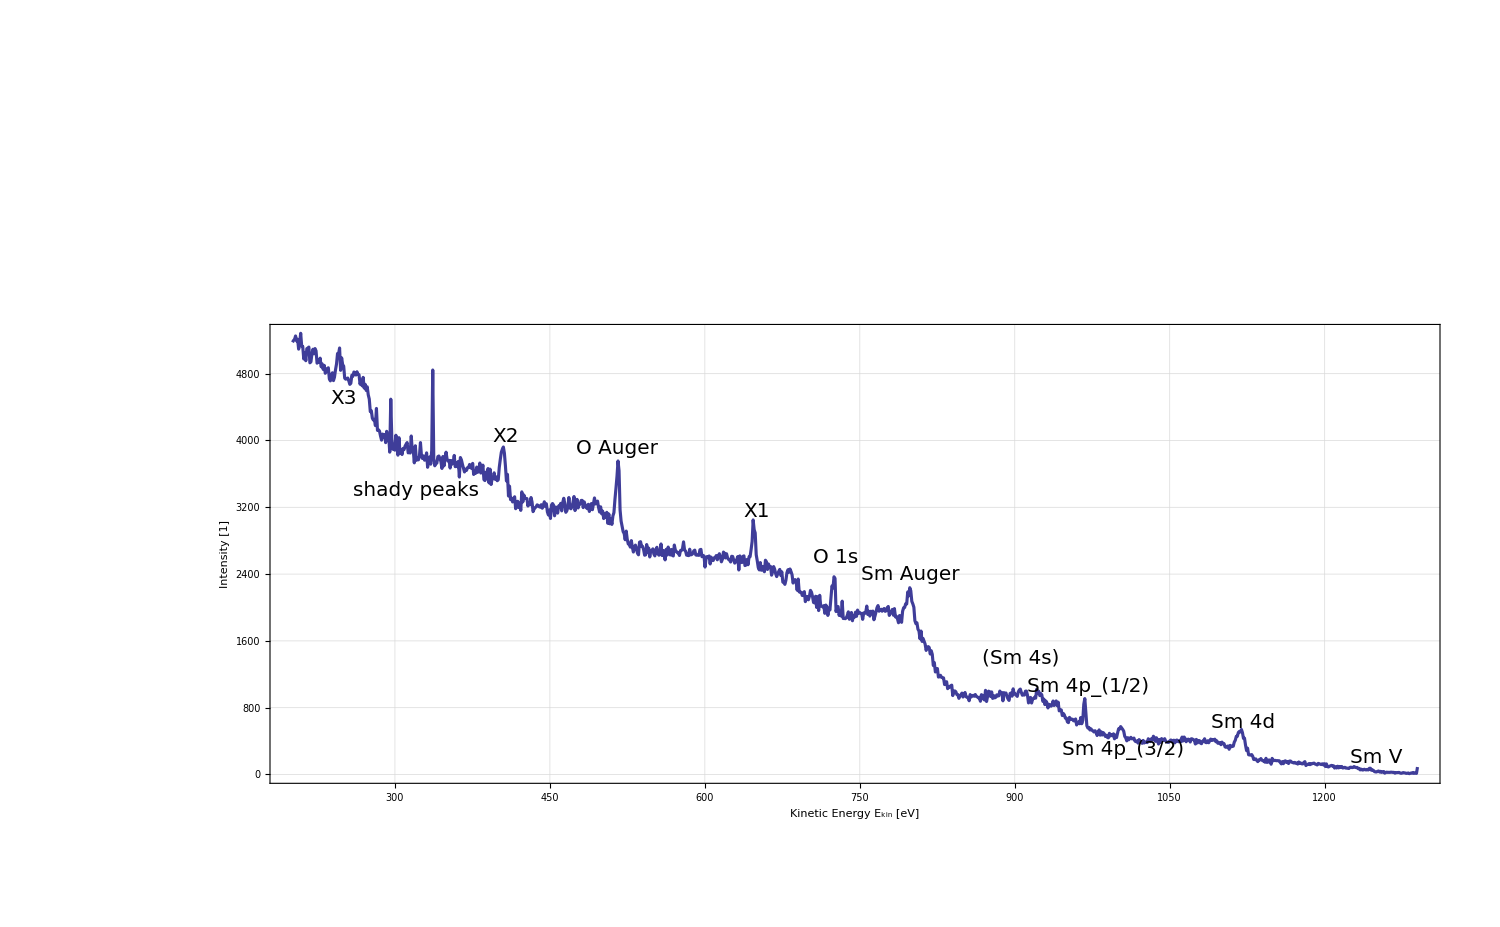

```mathematica
ListLinePlot[samarium⟦6⟧,niceStyleWoS,ImageSize->1500,PlotStyle->Thickness[0.0015],FrameTicks->{Automatic,Automatic,frameTickFunk[samarium⟦6⟧,1248,2],Automatic},Epilog->(Flatten[{Peak[#,"Sm V",0,200],Peak[#,"Sm 4d",129,620],Peak[#,"Sm 4p_(3/2)",245,290],Peak[#,"Sm 4p_(1/2)",279.5,1050],Peak[#,"(Sm 4s)",344,1400],Peak[#,"O 1s",523,2600],Peak[#,"O Auger",735,3900],Peak[#,"Sm 3d_(5/2)",1030,29000],Peak[#,"shady peaks",930,3400],Peak[#,"Sm Auger",451,2400],Peak[#,"X2",843,4050],Peak[#,"X3",1000,4500],,Peak[#,"X1",600,3150]}&/@{1250}]),FrameLabel->{Style["Kinetic Energy E_kin [eV]",Large],Style["Intensity [1]",Large],Style["Binding Energy E_B [eV]",Large],""}]
```

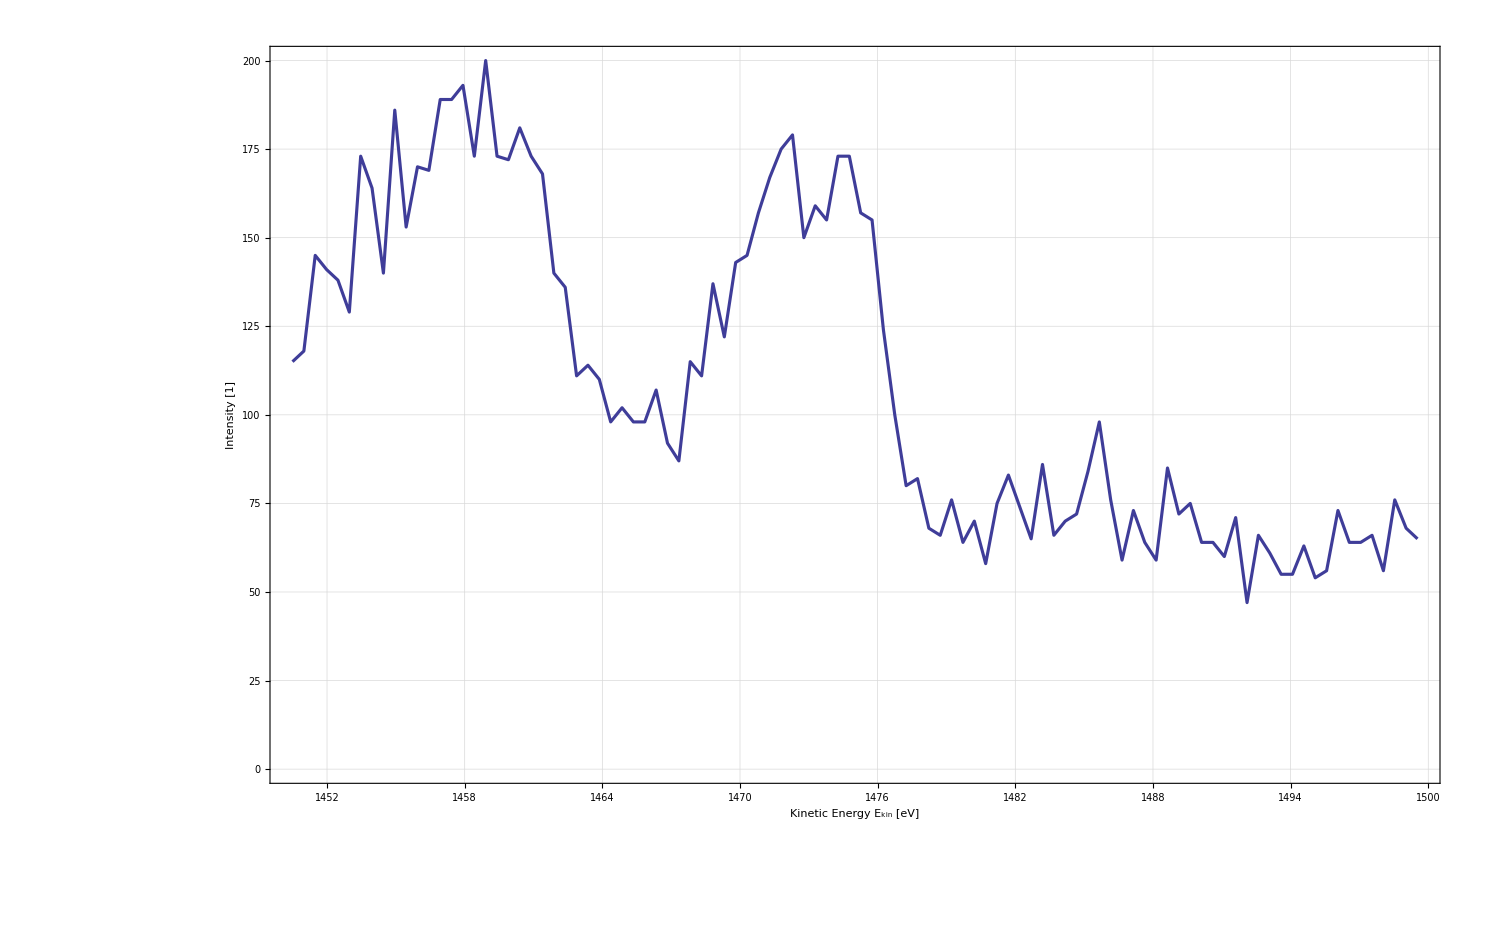

```mathematica
Show[ListLinePlot[samarium⟦2⟧,PlotStyle->Thickness[0.0015]],niceStyleWoS,ImageSize->1500,FrameTicks->{Automatic,Automatic,frameTickFunk[samarium⟦2⟧,1477,0.5],Automatic},FrameLabel->{Style["Kinetic Energy E_kin [eV]",Large],Style["Intensity [1]",Large],Style["Binding Energy E_B [eV]",Large],""}]
```

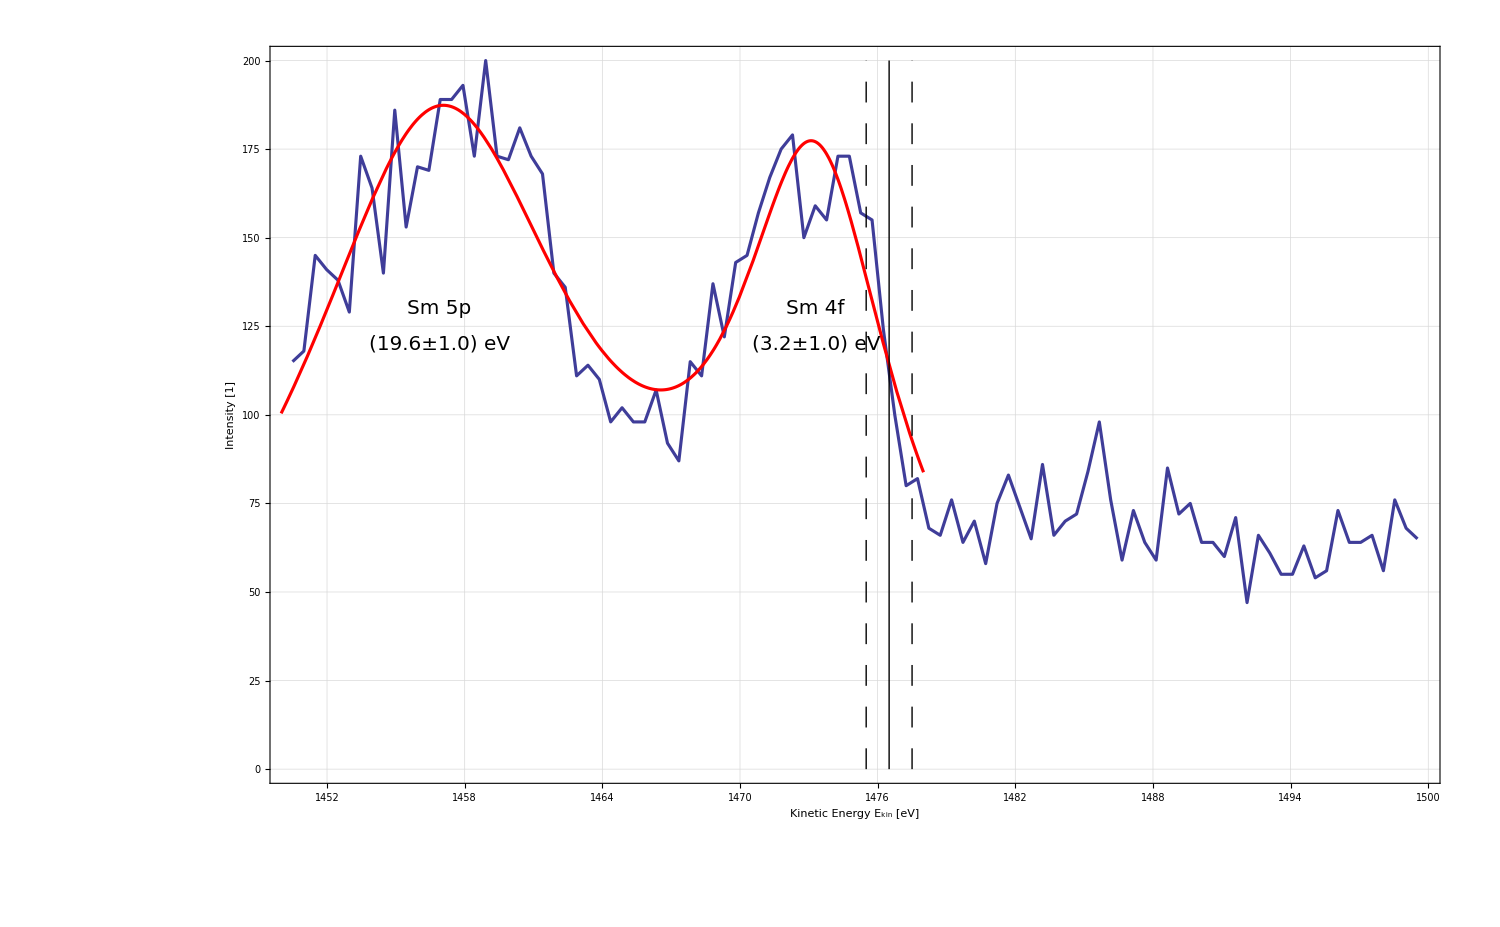

```mathematica
Show[ListLinePlot[samarium⟦2⟧,PlotStyle->Thickness[0.0015]],Plot[Normal[smfit],{x,1450,1478},PlotStyle->{Red,Thickness[0.0015]}],niceStyleWoS,ImageSize->1500,FrameTicks->{Automatic,Automatic,frameTickFunk[samarium⟦2⟧,1476.5,0.5],Automatic},Epilog->{Peak[1478,"Sm 4f",4.7,130],Peak[1478,"(3.2±1.0) eV",4.7,120],Peak[1478,"Sm 5p",21.1,130],Peak[1478,"(19.6±1.0) eV",21.1,120],Line[{{1476.5,0},{1476.5,200}}],{Dashing[0.01],Line[{{1475.5,0},{1475.5,200}}],Line[{{1477.5,0},{1477.5,200}}]}},FrameLabel->{Style["Kinetic Energy E_kin [eV]",Large],Style["Intensity [1]",Large],Style["Binding Energy E_B [eV]",Large],""}]
```

### Coin

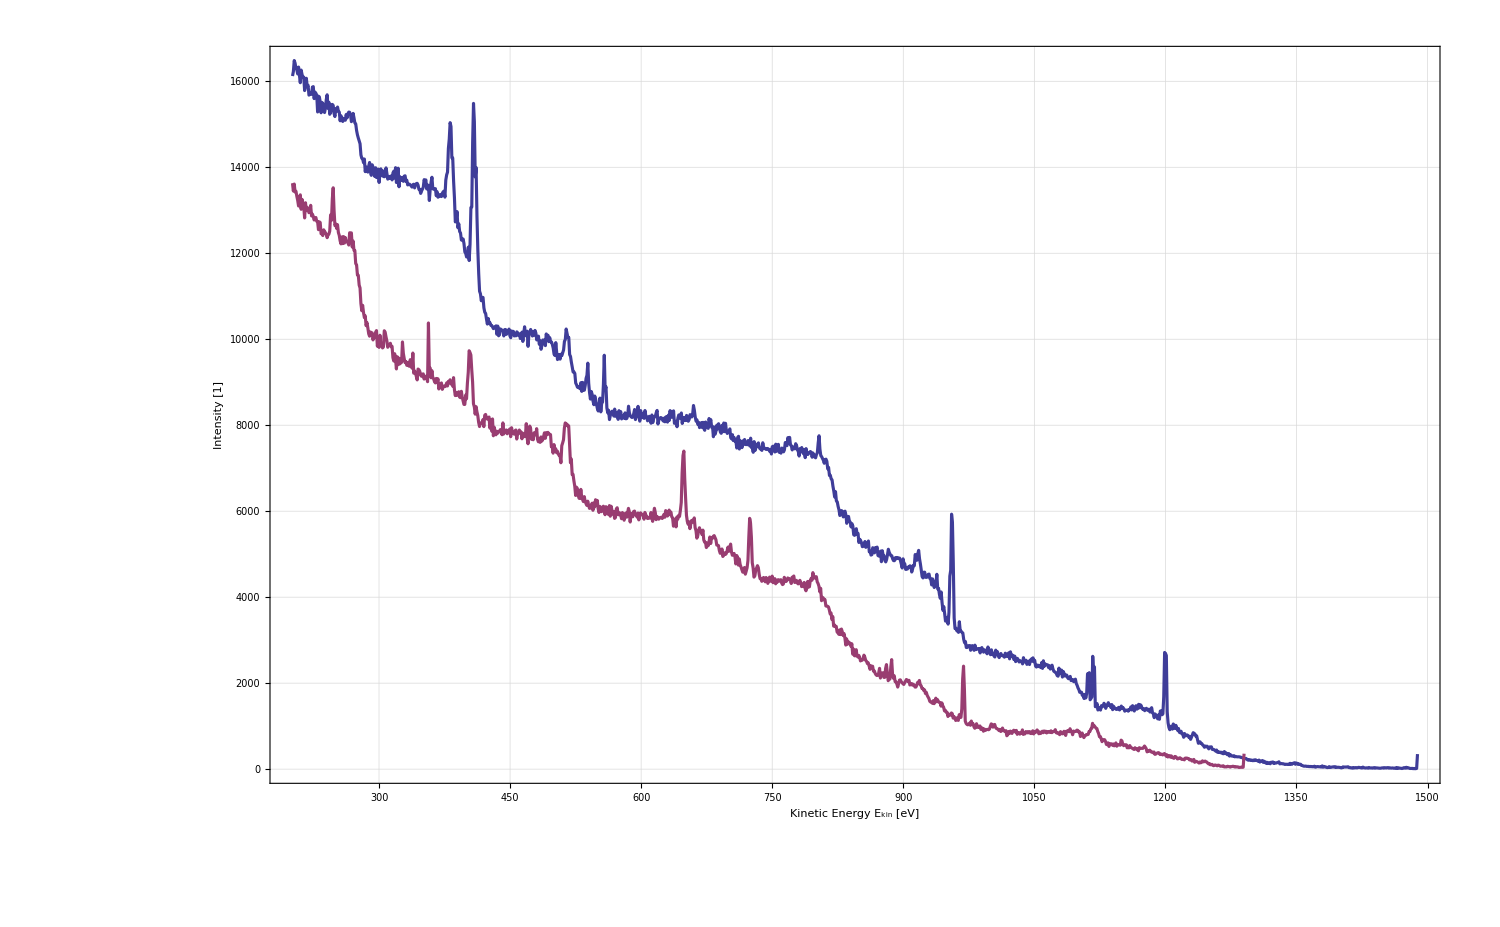

```mathematica
ListLinePlot[{coin⟦1⟧,coin⟦2⟧},niceStyleWoS,ImageSize->1500,PlotStyle->Thickness[0.0015],FrameLabel->{Style["Kinetic Energy E_kin [eV]",Large],Style["Intensity [1]",Large]}]
```

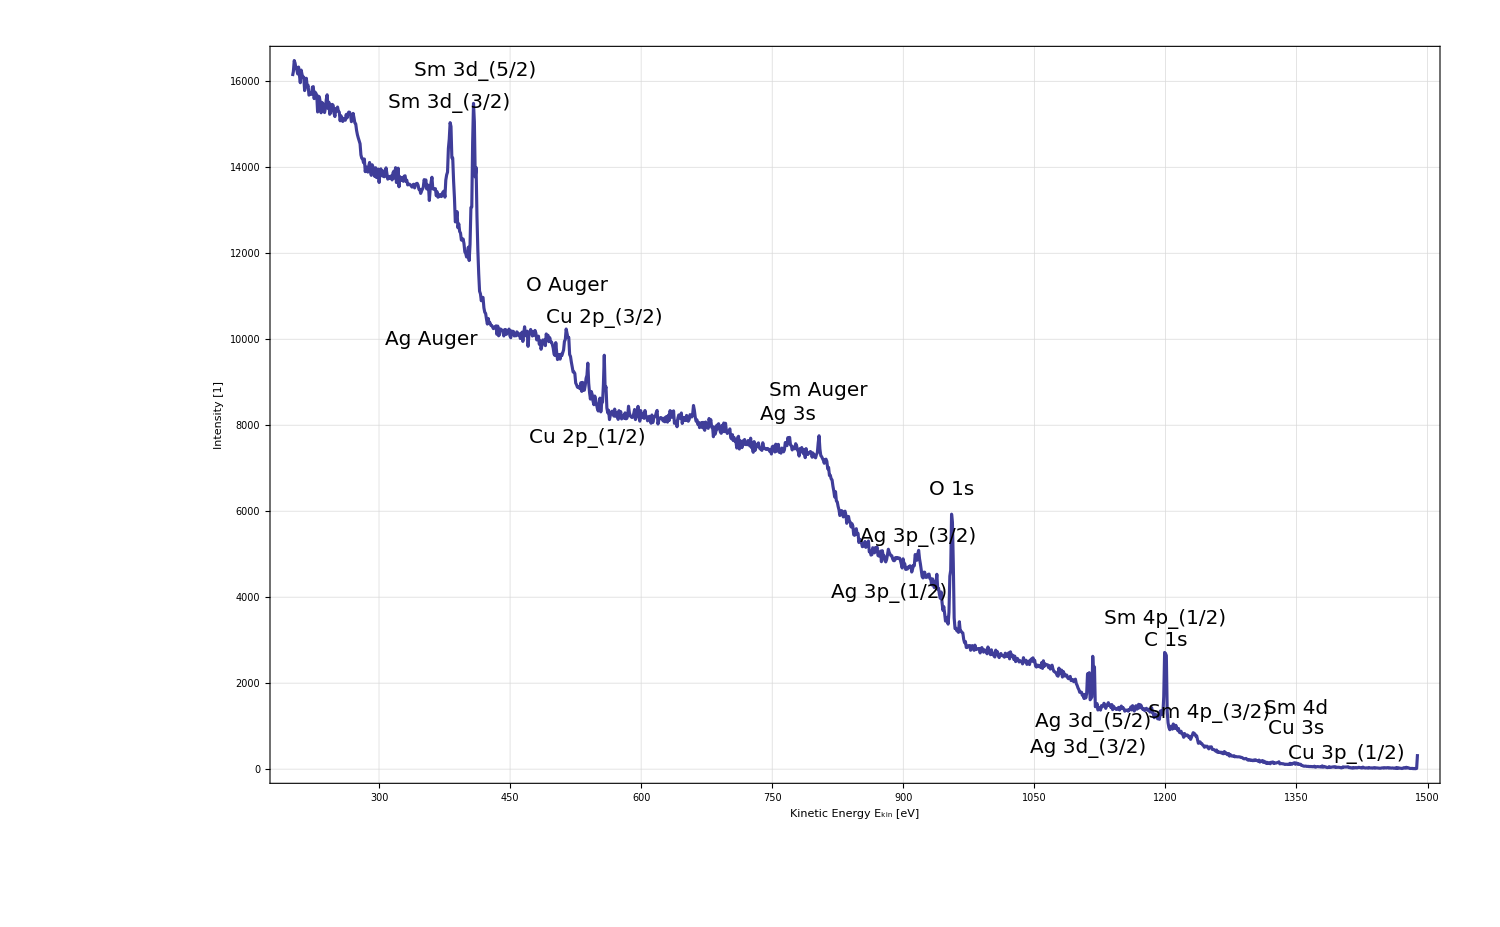

```mathematica
ListLinePlot[coin⟦1⟧,niceStyleWoS,ImageSize->1500,PlotStyle->Thickness[0.0015],FrameTicks->{Automatic,Automatic,frameTickFunk[coin⟦1⟧,1480,2],Automatic},Epilog->(Flatten[{Peak[#,"Cu 3p_(1/2)",73,350],Peak[#,"Cu 3s",130,950],Peak[#,"Sm 4d",130,1400],Peak[#,"Ag 3d_(5/2)",362.8,1100],Peak[#,"Ag 3d_(3/2)",368.2,500],Peak[#,"Ag 3p_(3/2)",563.5,5400],Peak[#,"Ag 3p_(1/2)",596.3,4100],Peak[#,"Sm 4p_(3/2)",230,1300],Peak[#,"Sm Auger",677,8800],Peak[#,"Ag 3s",712,8250],Peak[#,"Ag Auger",1120,10000],Peak[#,"C 1s",280,3000],Peak[#,"Sm 4p_(1/2)",280,3500],Peak[#,"O 1s",524.5,6500],Peak[#,"Cu 2p_(3/2)",922,10500],Peak[#,"Cu 2p_(1/2)",942,7700],Peak[#,"O Auger",965,11250],Peak[#,"Sm 3d_(5/2)",1069.5,16250],Peak[#,"Sm 3d_(3/2)",1100,15500]}&/@{1480}]),FrameLabel->{Style["Kinetic Energy E_kin [eV]",Large],Style["Intensity [1]",Large],Style["Binding Energy E_B [eV]",Large],""}]
```

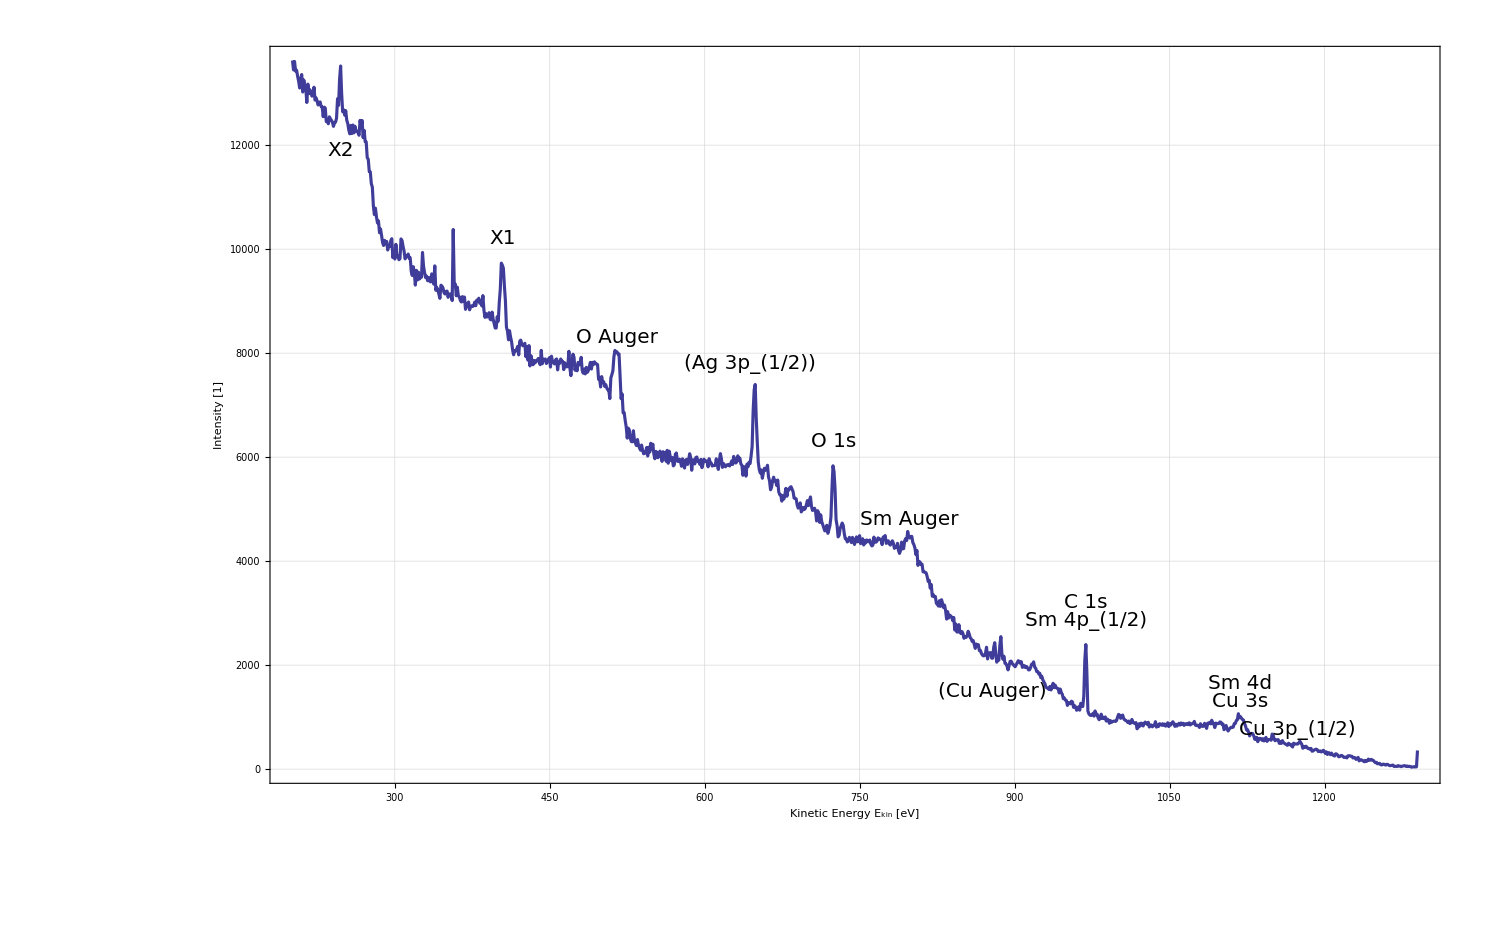

```mathematica
ListLinePlot[coin⟦2⟧,niceStyleWoS,ImageSize->1500,PlotStyle->Thickness[0.0015],FrameTicks->{Automatic,Automatic,frameTickFunk[coin⟦2⟧,1248,2],Automatic},Epilog->(Flatten[{Peak[#,"Cu 3p_(1/2)",74,750],Peak[#,"Cu 3s",130,1300],Peak[#,"Sm 4d",130,1650],Peak[#,"C 1s",279,3200],Peak[#,"Sm 4p_(1/2)",279,2840],Peak[#,"Sm Auger",450,4800],Peak[#,"(Cu Auger)",370,1500],Peak[#,"O 1s",523.5,6300],Peak[#,"(Ag 3p_(1/2))",604,7800],Peak[#,"O Auger",733,8300],Peak[#,"X1",844,10200],Peak[#,"X2",1000,11900]}&/@{1248}]),FrameLabel->{Style["Kinetic Energy E_kin [eV]",Large],Style["Intensity [1]",Large],Style["Binding Energy E_B [eV]",Large],""}]
```

## Playarea

### Same thing

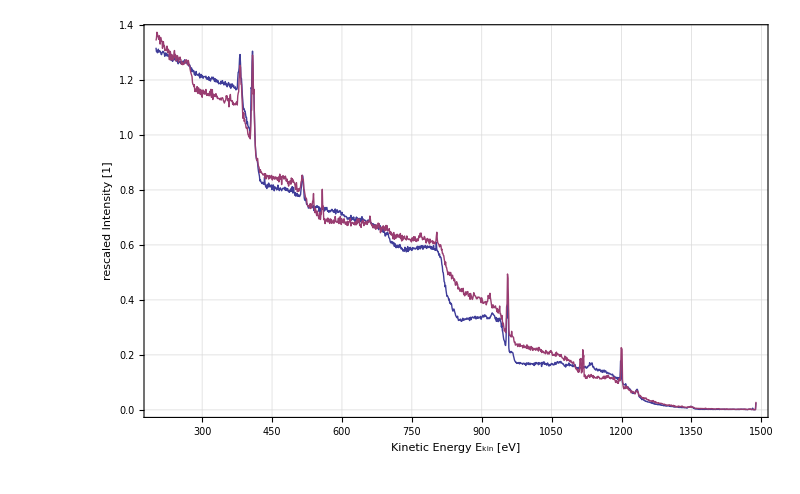

```mathematica
ListLinePlot[{{samarium⟦5⟧ᵀ⟦1⟧,1/22000*samarium⟦5⟧ᵀ⟦2⟧}ᵀ,{coin⟦1⟧ᵀ⟦1⟧,1/12000*coin⟦1⟧ᵀ⟦2⟧}ᵀ},niceStyleWoS,ImageSize->800,FrameLabel->{"Kinetic Energy E_kin [eV]","rescaled Intensity [1]"}]
```

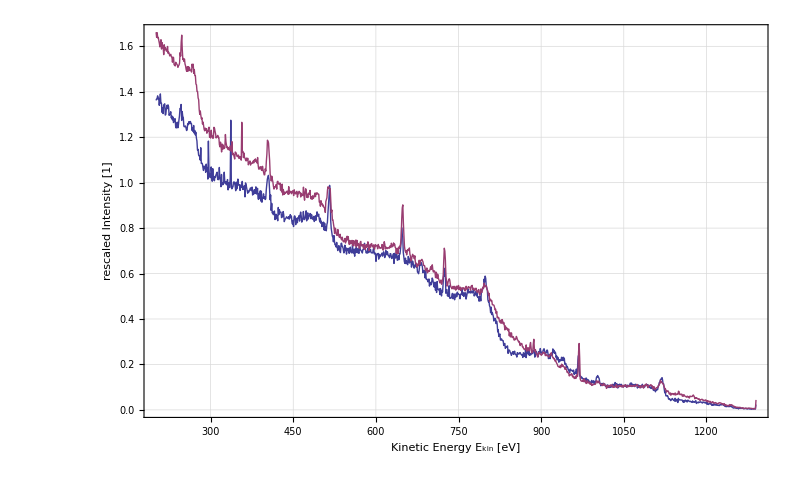

```mathematica
ListLinePlot[{{samarium⟦6⟧ᵀ⟦1⟧,1/3800*samarium⟦6⟧ᵀ⟦2⟧}ᵀ,{coin⟦2⟧ᵀ⟦1⟧,1/8200*coin⟦2⟧ᵀ⟦2⟧}ᵀ},niceStyleWoS,ImageSize->800,FrameLabel->{"Kinetic Energy E_kin [eV]","rescaled Intensity [1]"}]
```